### Optimal Response to a Passive Strategy

```mathematica
ClearAll["Global`*"]
```

b(t) = (-1+ⅇ^(-3 t))/(-1+1/ⅇ^3)

b(t) = 0.817574

Solution: {{a[t]→3.08333 ⅇ^(-3. t) (0.711078-0.711078 ⅇ^(3. t)+1. ⅇ^(3. t) t)}}

a(t) = 3.08333 ⅇ^(-3. t) (0.711078-0.711078 ⅇ^(3. t)+1. ⅇ^(3. t) t)

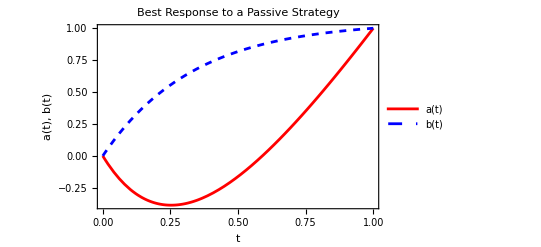

```mathematica
(*Define constants*)λ=5;κ=0.5;σ=3;

(*Define b(t) as a known function*)
CC=1.2;
(*b[t_]:=Sinh[σ t]/Sinh[σ]; *)    (* risk-averse *)
b[t_] := (Exp[-σ t] - 1) / (Exp[-σ] - 1); (* eager *)
(* b[t_] := t+CC*(0.25-(t-0.5)^2); *) (* parabolic *)
 beq[t_,κ_,λ_]:=((1-Exp[-κ t/3]) (Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1) λ)

(*Print b(t) to check its definition*)
Print["b(t) = ",b[t]];
Print["b(t) = ",b[t]/. t->0.5];

(*Define the differential equation for a(t)*)
solveForA[ξa_]:=Module[{eqns,bcs,sol,aSol},eqns={a''[t]==-(λ/2) (b''[t]+κ b'[t])};
bcs={a[0]==0,a[1]==1};
sol=DSolve[{eqns,bcs},a[t],t];
Print["Solution: ",sol];
aSol=a[t]/. sol[[1]];
aSol];

(*Example usage*)
ξa=1.5;
aSolution=solveForA[ξa];

(*Print a(t) to check its definition*)
Print["a(t) = ",aSolution];

(*Plot both a(t) and b(t) with b(t) as a dashed line*)
Plot[{aSolution,b[t]},{t,0,1},PlotLegends->{"a(t)","b(t)"},PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{{"a(t), b(t)","\!\(\*SubscriptBox[\(ξ\), \(a\)]\) = "<>ToString[ξa]<>", σ="<>ToString[σ]},{"t","κ="<>ToString[κ]<>", λ="<>ToString[λ]}},PlotLabel->"Best Response to a Passive Strategy",PlotRange->All]
```

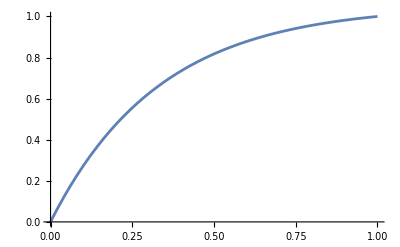

```mathematica
Plot[(-1+ⅇ^(-3 t))/(-1+1/ⅇ^3), {t, 0, 1}]
```

```mathematica
Print[b[t]]
```

(-1+ⅇ^(-3 t))/(-1+1/ⅇ^3)

#### Parabolic function

```mathematica
f [t_, c_]= t  (t - c) / (1 - c);
D[f[t,c], t]
```

t/(1-c)+(-c+t)/(1-c)

```mathematica
Manipulate[Plot[f[t,c],{t,0,1}],{c,-1,2}]
```

### Eager Strategy

```mathematica
f [t_, σ_]:= (Exp[-σ t] - 1) / (Exp[-σ] - 1)
fPrime [t_, σ_]= D[f[t,σ], t ]
N[{f[1, 3], fPrime[1, 3]}]
```

-(3 ⅇ^(-3 t))/(-1+1/ⅇ^3)

{1.,0.157187}

```mathematica
Manipulate[Plot[f[t,σ],{t,0,1}],{σ,-10,10}]
```